## Define Hamiltonian and useful functions

```mathematica
Clear[findEvolutionOperator4D, funcs, ψ0, equations, Uuncut]
findEvolutionOperator4D[HamIn_, Tmax_, acc_:10]:=(
isToKeep = {1, 2, 3, 5, 6};
statesToKeep = Table[8*i + j - 8, {i, isToKeep}, {j, isToKeep}] // Flatten;
Ham = HamIn[[statesToKeep, statesToKeep]];

funcs=Array[ψ[#2 + 4*(#1- 1)][t]&,{Length[statesToKeep], 4}];
ψ0 = Table[0, {i, Length[statesToKeep]}, {j, 4}];
ψ0[[1, 1]] = 1.;
ψ0[[2, 2]] = 1.;
ψ0[[1 + Length[isToKeep], 3]] = 1.;
ψ0[[2 + Length[isToKeep], 4]] = 1.;


equations=Flatten@Join[Thread[Ham.funcs == ⅈ*D[funcs,t]],Thread[funcs==ψ0/.t->0]];
Uuncut = NDSolveValue[equations,funcs,{t,0,Tmax}, AccuracyGoal->acc, PrecisionGoal->acc, EvaluationMonitor:>showStatus["Tmax = "<>ToString[AccountingForm[Tmax]]<>"          t = "<>ToString[CForm[t]]]];
Uuncut[[{1, 2, 1 + Length[isToKeep], 2 + Length[isToKeep]}]]
)

ClearAll[debug];
SetAttributes[debug,HoldAll];
debug[code_]:=Internal`InheritedBlock[{Message},Module[{inMessage},Unprotect[Message];
Message[args___]/;!MatchQ[First[Hold[args]],_$Off]:=Block[{inMessage=True},Print[{Shallow/@Replace[#,HoldForm[f_[___]]:>HoldForm[f],1],Style[Map[Short,Last[#],{2}],Red]}&@Drop[Drop[Stack[_],-7],4]];
Message[args];
Throw[$Failed,Message];]/;!TrueQ[inMessage];
Protect[Message];];
Catch[StackComplete[code],Message]]

CZangle[M_] := (
z = (M[[4, 4]]*M[[1, 1]])/(M[[2, 2]]*M[[3, 3]]);
ArcTan[Re[z], Im[z]]
)
Zangle[M_] := (
z = M[[2, 2]]/M[[1, 1]];
ArcTan[Re[z], Im[z]]
)
```

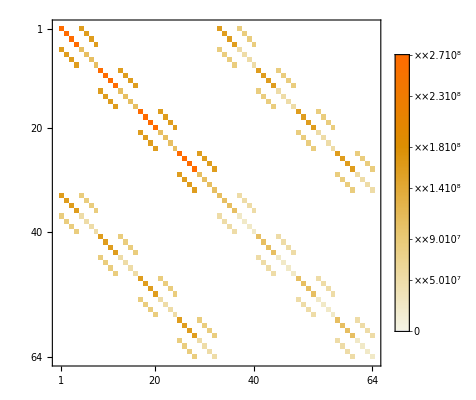

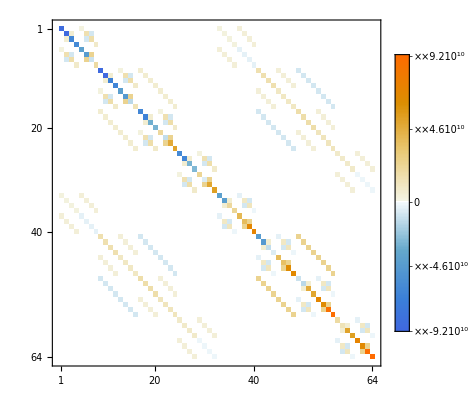

```mathematica
Vdip = (d*e)^2/(4*π*8.85418782×10^-12*11.7*dDip^3*h/(2π));
Hdip = Vdip*TProduct[TProduct[ii, σI, σI], TProduct[ii, σI, σI]];

H2 = TProduct[Hexact, IdentityMatrix[8]] + TProduct[IdentityMatrix[8], Hexact] + Hdip;

setVariables[]

ΔE = 2000;

MatrixPlot[Hdip, PlotLegends->True]

Bamp[t_] := 0
Eamp[t_] := 0
MatrixPlot[H2, PlotLegends->True]

clearVariables[]
```

## Look at single qubit evolution

```mathematica
(*setVariables[]

Tmax = 10^-6;

ΔE = 2000;

Eamp[t_] := 30*cosWindow[t, Tmax/3, Tmax];
ωE = 2*π*(ϵ0 - A/4 + A*dState[[1]]^2) - 2*π*20*10^6;

(* turn off oscillatin' magnetic field *)
Bamp[t_] := 0
ωB = ωE;

statesInOrder[Hcorrected /. t->Tmax/2] // MatrixForm

Hcorrected[[1, 5]]

Vdip*((statesInOrder[Hcorrected /. t->Tmax/2][[2, 2]])^2 - (statesInOrder[Hcorrected /. t->Tmax/2][[1, 1]])^2)^2 / (2*π)*)

(*U = findEvolutionOperator2D[Hcorrected, Tmax];

(*Abs[Uax[[1]][[5]]]^2 /. t->Tmax/2
Abs[Uax[[2]][[6]]]^2 /. t->Tmax/2*)

Evaluate@Table[Max[Abs[Uuncut[[i]][[1]]]^2, 10^-8], {i, 8}];
LogPlot[{%[[1]], %[[2]], %[[3]], %[[4]], %[[5]], %[[6]], %[[7]], %[[8]]}, {t, 0,  Tmax}, PlotLegends->basisGE, PlotLabel->"Probabilities by t, starting in |gdd>"]

Evaluate@Table[Max[Abs[Uuncut[[i]][[2]]]^2, 10^-8], {i, 8}];
LogPlot[{%[[1]], %[[2]], %[[3]], %[[4]], %[[5]], %[[6]], %[[7]], %[[8]]}, {t, 0,  Tmax}, PlotLegends->basisGE, PlotLabel->"Probabilities by t, starting in |gdu>"]*)


clearVariables[]
```

## Estimate theoretical transition rate

```mathematica
setVariables[]

ΔE = 2000;
Ea = 40;
Eamp[t_] := Ea
ωE = 2*π*(ϵ0 + A/4 - A*dState[[1]]^2/2) + 2*π*5*10^6;
Bamp[t_] := 0

(statesInOrder[Hcorrected] // Transpose) // MatrixForm
Λge.(statesInOrder[Hcorrected] // Transpose) // MatrixForm
(1/(2π))*Vdip*(((Λge.(statesInOrder[Hcorrected] // Transpose))[[2, 2]])^2 - ((Λge.(statesInOrder[Hcorrected] // Transpose))[[1, 1]])^2)^2

clearVariables[]
```

Eigensystem::eivec0: Unable to find all eigenvectors.

(-1.01122 | 0 | 0 | 0 | -1.01122 | 0 | 0 | 0
0. | 0 | 0 | 0 | 0. | 0 | 0 | 0
0. | 0 | 0 | 0 | 0. | 0 | 0 | 0
0. | 0 | 0 | 0 | 0. | 0 | 0 | 0
1. | 0 | 0 | 0 | 1. | 0 | 0 | 0
0. | 0 | 0 | 0 | 0. | 0 | 0 | 0
0. | 0 | 0 | 0 | 0. | 0 | 0 | 0
0. | 0 | 0 | 0 | 0. | 0 | 0 | 0)

Eigensystem::eivec0: Unable to find all eigenvectors.

(-1.27984 | 0. | 0. | 0. | -1.27984 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.62015 | 0. | 0. | 0. | 0.62015 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

Eigensystem::eivec0: Unable to find all eigenvectors.

General::stop: Further output of Eigensystem::eivec0 will be suppressed during this calculation.

1.43719×10^8

## Optimize a CZ gate

### Helper functions

```mathematica
angle[z_] := ArcTan[Re[z], Im[z]]
CZangle[M_] := (
z = (M[[4, 4]]*M[[1, 1]])/(M[[2, 2]]*M[[3, 3]]);
ArcTan[Re[z], Im[z]]
)
fidelityToCZWithLocalZs[M_] := (
angles = Table[ArcTan[Re[u], Im[u]], {u, Diagonal[M]}];

U2afterGates = U2*E^(-ⅈ*angles[[1]]) /. t->Tmax;

pZ = {{1, 0}, {0, E^(-ⅈ*(angles[[2]] - angles[[1]]))}};
U2afterGates = TProduct[pZ, pZ].U2afterGates;

CZ = DiagonalMatrix[{1, 1, 1, -1}];

fidelity[ConjugateTranspose[CZ].U2afterGates]
)

Clear[fidelityCZ];
fidelityCZ[EaIn_?NumericQ, acc_:10] := (
Clear[Eamp];
Eamp[t_] := EaIn*tanhWindow[t,Tmax/5,Tmax]^2 ;

Ubase = MatrixExp[-ⅈ*t*DiagonalMatrix[energiesInOrder[HcorrectedStatic]]];

U2 = (ConjugateTranspose[TProduct[Ubase, Ubase]])[[{1, 2, 9, 10}, {1, 2, 9, 10}]].findEvolutionOperator4D[H2, acc];

F = fidelityToCZWithLocalZs[U2 /. t->Tmax];

Print[{F, CZangle[U2 /. t->Tmax], {ΔE, B0, EaIn, 0, ωE, ωB, Tmax}}];

F
)
```

### Optimization - will take hours to run

```mathematica
(*setVariables[]

ΔE = -3000;

Tmax = 1000*10^-9;

(* set Eac *)
ωE = 2*π*(ϵ0 + A/4 - (A*dState[[1]]^2/2)) - 2*π*1.7*10^7;
(*Eamp[t_] := 20*tanhWindow[t,Tmax/5, Tmax]^2 ;*)

(* turn off oscillatin' magnetic field *)
ωB = (ωB + ωE)/2;
Bamp[t_] := 0

Clear[map]
map[x_, a_, b_] := a + (b - a)*x // Re

TimeConstrained[(
bestSoFar = 0;
bestParameters = {};

NMaximize[
{
fidelityCZ[
map[x1, 10, 60]
],
0 < x1 < 1
},
{{x1, .3, .7}},
Method->{"NelderMead", "RandomSeed"->RandomInteger[{0, 10000}]},
MaxIterations->10000
]

), 60*60*10
]

clearVariables[]*)
```

### Generate a Spectrum of C-phase Gates

```mathematica
CphaseParameters[T_] := (
setVariables[];

Tmax = T;

T1 = 5*10^-9;
T2 = Tmax - 2*T1;
T3 = Min[T2/2, 300*10^-9];

Clear[ΔE];

Ea = 40*Min[1, (T3/(300*10^-9))^2];
Eamp[t_] := Ea*cosWindow[t - T1, T3, T2];
ωE = 2*π*(ϵ0 + A/4 - A*dState[[1]]^2/2) - 2*π*10*10^6 /. ΔE->2000;

Bamp[t_] := 0;
ωB = (ωB + ωE)/2;

ΔE = 10000 - 8000*twoPointWindow[t, T1, Tmax, 1];

Ubase = MatrixExp[-ⅈ*t*(H2[[{1, 2, 9, 10}, {1, 2, 9, 10}]] /. t->0)];

U = findEvolutionOperator4D[H2, Tmax];

Ufinal = ConjugateTranspose[Ubase].U /. t->Tmax;
ϕ = CZangle[Ufinal];
ϕz = -Zangle[Ufinal];

pNonAd = 1 - Sum[Abs[Ufinal[[i, i]]]^2, {i, 4}]/4;

Print[{Tmax, ϕ, ϕz, pNonAd}];
clearVariables[];

{ϕ, ϕz, pNonAd}

)

CphaseParams = {};
Do[AppendTo[CphaseParams, Join[{T}, CphaseParameters[T]]], {T, 0, 1000*10^-9, 50*10^-9}];
CphaseParams
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of 5.76524×10^10+ωB.

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Part::partw: Part 4 of ConjugateTranspose[Ubase].U does not exist.

Part::partd: Part specification (ConjugateTranspose[Ubase].U)⟦2,2⟧ is longer than depth of object.

Part::partw: Part 3 of ConjugateTranspose[Ubase].U does not exist.

Part::partd: Part specification (ConjugateTranspose[Ubase].U)⟦2,2⟧ is longer than depth of object.

Part::partw: Part 4 of ConjugateTranspose[Ubase].U does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification (ConjugateTranspose[Ubase].U)⟦2,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{0,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)}

{1/20000000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)}

{1/10000000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)}

{3/20000000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)}

{1/5000000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)}

{1/4000000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)}

{3/10000000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)}

{7/20000000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)}

{1/2500000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)}

{9/20000000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)}

{1/2000000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)}

{11/20000000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)}

{3/5000000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)}

{13/20000000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)}

{7/10000000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)}

{3/4000000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)}

{1/1250000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)}

{17/20000000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)}

{9/10000000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)}

{19/20000000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)}

{1/1000000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)}

{{0,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)},{1/20000000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)},{1/10000000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)},{3/20000000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)},{1/5000000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)},{1/4000000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)},{3/10000000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)},{7/20000000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)},{1/2500000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)},{9/20000000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)},{1/2000000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)},{11/20000000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)},{3/5000000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)},{13/20000000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)},{7/10000000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)},{3/4000000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)},{1/1250000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)},{17/20000000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)},{9/10000000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)},{19/20000000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)},{1/1000000,ArcTan[Re[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)],Im[(Ubase (ConjugateTranspose[Ubase].U)⟦4,4⟧)/((ConjugateTranspose[Ubase].U)⟦2,2⟧ (ConjugateTranspose[Ubase].U)⟦3,3⟧)]],-ArcTan[Re[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase],Im[((ConjugateTranspose[Ubase].U)⟦2,2⟧)/Ubase]],1+1/4 (-Abs[Ubase]^2-Abs[(ConjugateTranspose[Ubase].U)⟦2,2⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦3,3⟧]^2-Abs[(ConjugateTranspose[Ubase].U)⟦4,4⟧]^2)}}

```mathematica
unravel[input_] := (
output = input;
Do[(
If[output[[i + 1]] - output[[i]] > π, output[[i + 1;;]] = output[[i + 1;;]] - 2π];
If[output[[i + 1]] - output[[i]] < -π, output[[i + 1;;]] = output[[i + 1;;]] + 2π];
),{i, Length[input] - 1}
];
output
)
Do[
CphaseParams[[All, i]] = unravel[CphaseParams[[All, i]]],
{i, {2, 4}}];

ϕFn = Interpolation[CphaseParams[[All, {1, 2}]]];


Figure[{
FigurePanel[{
FigGraphics[
Plot[ϕFn[T*10^-9], {T, 0, 1000}, PlotStyle->Blue]
]
},
XPlotRange->{0, 700}, XFrameLabel->"T (ns)",
YPlotRange->{-2π - .5, 0 + .3}, YFrameLabel->"ϕ", YTicks->LinTicksPi[-3π, π, π/2, 4, {"-3π", "-5π/2", "-2π", "-3π/2", "-π", "-π/2", "0", "π/2", "π"}]
];
},CanvasSize->{5,2}]

Export["CZgateAngles.eps", %]
```

-Graphics-

CZgateAngles.eps